```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

E:\scratch\archive\Ag_PVP10\para\111Ag\pmf_curve\equilibrate\1_NVT

```mathematica
numbatom=2415;
numbatomtype = 16;
```

```mathematica
masslist={1.008,1.008,1.008,1.008,12.011,12.011,12.011,12.011,12.011,14.007,15.9994,1.008,1.008,12.011,15.9994,107.8682};
```

```mathematica
masslist[[11]] (*Atom type of O in PVP molecule*)
```

15.9994

```mathematica
timeprod=2000;
timestepthermo=2000;
timesteptraj=10000;
(*Production time*)
```

```mathematica
(*Atoms per molecules, PVP10 = 175, PVP = 90, 2PDO = 13, MB3 = 16, EPD = 19*)
(*DON'T FORGET TO MANUALLY EDIT EVERYTIME*)
sizepvp=175;
numbpvp=1;
```

```mathematica
firstpvpatomid=2241;
lastpvpatomid=2415;
```

```mathematica
lz=81;
```

```mathematica
(*pvpatomtypeseq={10,8,8,11,9,10,8,8,11,9};*)
```

```mathematica
pvpatomtypeseq={8,4,4,4,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,8,4,4,4,6,2,10,5,11,9,1,1,9,1,1,9,1,1};
```

```mathematica
Length[pvpatomtypeseq]
```

175

```mathematica
oxypos=Flatten[Position[pvpatomtypeseq,11]]
```

{12,29,46,63,80,97,114,131,148,166}

```mathematica
masslist[[pvpatomtypeseq]]
```

{12.011,1.008,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,1.008,12.011,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008}

```mathematica
masslistrep=Flatten[Table[masslist[[pvpatomtypeseq]],{i,numbpvp}]];
```

```mathematica
IfBelow[x_]:=If[x<0,1,0];
IfAbove[x_]:=If[x>lz,-1,0];
```

```mathematica
firstagatomid=1;
lastagatomid=2240;
```

```mathematica
readtraj[]:=
Module[{},
trajfilename="traj_nvt.lammpstrj";
traj=OpenRead[trajfilename];
Find[traj,"TIMESTEP"];
timestep=Read[traj,Number];
timesteptemp=timestep;
pvpcomtemp=Reap[
While[!(timesteptemp===EndOfFile),
Find[traj,"ATOMS id mol type"];
atompositiontemp=Sort[ReadList[traj,{Number,Number,Number,Number,Number,Number, Number,Number,Number},numbatom]];
atompositiontemp[[All,1]]=timesteptemp;
pvppositiontemp=atompositiontemp[[firstpvpatomid;;lastpvpatomid]];
pvppositiontemp[[All,7]]=pvppositiontemp[[All,9]]*lz+pvppositiontemp[[All,6]];
pvpcomtemp=Total[Partition[pvppositiontemp[[All,7]]*masslistrep,sizepvp],{2}]/Total[masslist[[pvpatomtypeseq]]];
Sow[pvpcomtemp];
timestepdiff=timesteptemp-timesteptemp2;
timesteptemp2=timesteptemp;
Find[traj,"TIMESTEP"];
timesteptemp = Read[traj,Number];
]
][[2,1]];
Close[traj];
traj=OpenRead[trajfilename];
Find[traj,"TIMESTEP"];
timestep=Read[traj,Number];
timesteptemp=timestep;
oxytemp=Reap[
While[!(timesteptemp===EndOfFile),
Find[traj,"ATOMS id mol type"];
atompositiontemp=Sort[ReadList[traj,{Number,Number,Number,Number,Number,Number, Number,Number,Number},numbatom]];
atompositiontemp[[All,1]]=timesteptemp;
pvppositiontemp=atompositiontemp[[firstpvpatomid;;lastpvpatomid]];
pvppositiontemp[[All,7]]=pvppositiontemp[[All,9]]*lz+pvppositiontemp[[All,6]];
oxytemp=Partition[pvppositiontemp[[All,7]],sizepvp][[All,oxypos]];
Sow[oxytemp];
timestepdiff=timesteptemp-timesteptemp2;
timesteptemp2=timesteptemp;
Find[traj,"TIMESTEP"];
timesteptemp = Read[traj,Number];
]
][[2,1]];
Close[traj];
traj=OpenRead[trajfilename];
Find[traj,"TIMESTEP"];
timestep=Read[traj,Number];
timesteptemp=timestep;
agposition=Reap[
While[!(timesteptemp===EndOfFile),
Find[traj,"ATOMS id mol type"];
atompositiontemp=Sort[ReadList[traj,{Number,Number,Number,Number,Number,Number, Number,Number,Number},numbatom]];
atompositiontemp[[All,1]]=timesteptemp;
agpositiontemp=atompositiontemp[[firstagatomid;;lastagatomid]];
agpositiontemp[[All,7]]=agpositiontemp[[All,9]]*lz+agpositiontemp[[All,6]];
Sow[agpositiontemp];
timestepdiff=timesteptemp-timesteptemp2;
timesteptemp2=timesteptemp;
Find[traj,"TIMESTEP"];
timesteptemp = Read[traj,Number];
]
][[2,1]];
agposition=Partition[Flatten[agposition],9];
agztemp=agposition[[All,7]];
Close[traj];
];
```

```mathematica
readtraj[];
```

```mathematica
pvpcom=pvpcomtemp;
oxy=oxytemp;
agz=agztemp;
```

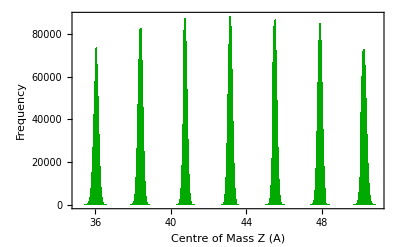

```mathematica
AgComzHist=Histogram[agz,300,ChartStyle->Darker[Green],Frame->True,FrameLabel->{"Centre of Mass Z (A)","Frequency"},LabelStyle->Directive[FontSize->15]]
```

```mathematica
topAgsurface=Mean[Select[agz,#<37&]]
```

36.0561

```mathematica
oxyfromsurf=topAgsurface-oxy;
pvpcomfromsurf=topAgsurface-pvpcom;
```

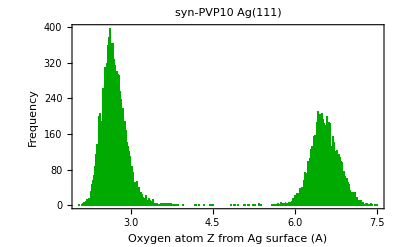

```mathematica
OxyHist=Histogram[Flatten[oxyfromsurf],300,ChartStyle->Darker[Green],Frame->True,FrameLabel->{"Oxygen atom Z from Ag surface (A)","Frequency"},LabelStyle->Directive[FontSize->15],PlotLabel->"syn-PVP10 Ag(111)"]
```

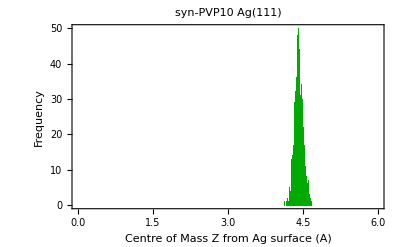

```mathematica
ComzHist=Histogram[Flatten[pvpcomfromsurf],100,ChartStyle->Darker[Green],Frame->True,FrameLabel->{"Centre of Mass Z from Ag surface (A)","Frequency"},LabelStyle->Directive[FontSize->15],PlotLabel->"syn-PVP10 Ag(111)",PlotRange->{{0,6},Full}]
```

```mathematica
CreateDirectory["density"];
```

CreateDirectory::filex: "E:\\scratch\\archive\\Ag_PVP10\\para\\111Ag\\pmf_curve\\equilibrate\\1_NVT\\density\\" already exists.

```mathematica
Export["density/Hist_Comz_syn111.png",ComzHist,ImageResolution->300];
Export["density/Hist_oxy_syn111.png",OxyHist,ImageResolution->300];
```

```mathematica
SetDirectory["E:\\scratch\\archive\\Ag_PVP10\\isotac-para\\111Ag\\pmf_curve\\equilibrate\\1_NVT"]
```

E:\scratch\archive\Ag_PVP10\isotac-para\111Ag\pmf_curve\equilibrate\1_NVT

```mathematica
readtraj[];
```

```mathematica
pvpcomiso=pvpcomtemp;
oxyiso=oxytemp;
agziso=agztemp;
```

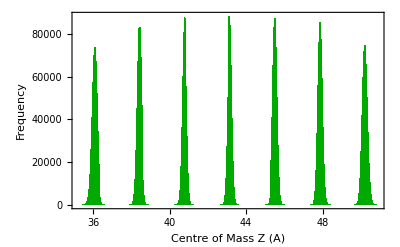

```mathematica
AgComzHistsyn=Histogram[agziso,300,ChartStyle->Darker[Green],Frame->True,FrameLabel->{"Centre of Mass Z (A)","Frequency"},LabelStyle->Directive[FontSize->15]]
```

```mathematica
topAgsurfaceiso=Mean[Select[agziso,#<37&]]
```

36.0604

```mathematica
oxyfromsurfiso=topAgsurfaceiso-oxyiso;
pvpcomfromsurfiso=topAgsurfaceiso-pvpcomiso;
```

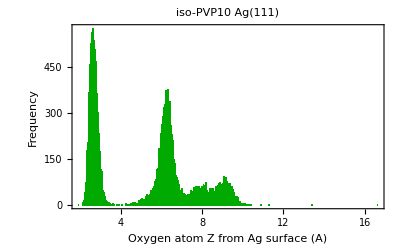

```mathematica
OxyHistiso=Histogram[Flatten[oxyfromsurfiso],300,ChartStyle->Darker[Green],Frame->True,FrameLabel->{"Oxygen atom Z from Ag surface (A)","Frequency"},LabelStyle->Directive[FontSize->15],PlotLabel->"iso-PVP10 Ag(111)"]
```

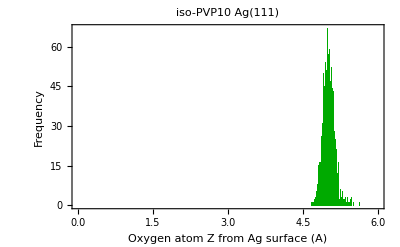

```mathematica
ComzHistiso=Histogram[Flatten[pvpcomfromsurfiso],300,ChartStyle->Darker[Green],Frame->True,FrameLabel->{"Oxygen atom Z from Ag surface (A)","Frequency"},LabelStyle->Directive[FontSize->15],PlotLabel->"iso-PVP10 Ag(111)",PlotRange->{{0,6},Full}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["density/Hist_Comz_iso111.png",ComzHistiso,ImageResolution->100];
Export["density/Hist_Oxy_iso111.png",OxyHistiso,ImageResolution->100];
```

```mathematica
Total[Flatten[oxyfromsurf]]
```

63739.8

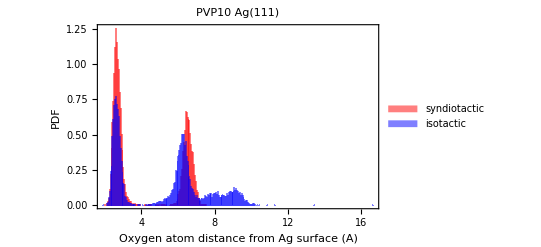

```mathematica
OxyHistComp=Histogram[{Flatten[oxyfromsurf],Flatten[oxyfromsurfiso]},
300,"PDF",PlotLabel->"PVP10 Ag(111)",
ChartStyle->{Red,Blue},
ChartLegends->Placed[{"syndiotactic","isotactic"},Bottom],
Frame->True,
FrameLabel->{"Oxygen atom distance from Ag surface (A)","PDF"},
LabelStyle->Directive[FontSize->15]]
```

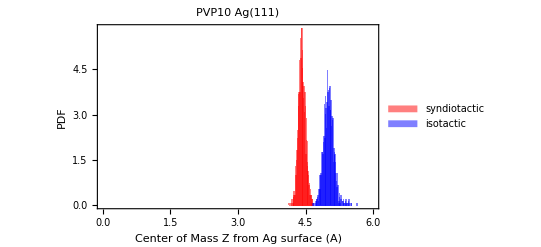

```mathematica
ComzHistComp=Histogram[{Flatten[pvpcomfromsurf],Flatten[pvpcomfromsurfiso]},
300,"PDF",PlotLabel->"PVP10 Ag(111)",
ChartStyle->{Red,Blue},
ChartLegends->Placed[{"syndiotactic","isotactic"},Bottom],
Frame->True,
FrameLabel->{"Center of Mass Z from Ag surface (A)","PDF"},
LabelStyle->Directive[FontSize->15],PlotRange->{{0,6},Full}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["density/Hist_Comz_Compare_111.png",ComzHistComp,ImageResolution->100];
Export["density/Hist_Oxy_Compare_111.png",OxyHistComp,ImageResolution->100];
```

```mathematica
SetDirectory["E:\\scratch\\archive\\Ag_PVP10\\para\\100Ag\\pmf_curve\\equilibrate\\1_NVT"];
numbatom=1903;
firstpvpatomid=1729;
lastpvpatomid=1903;
firstagatomid=1;
lastagatomid=1728;
```

```mathematica
readtraj[];
```

```mathematica
pvpcomsyn100=pvpcomtemp;
oxysyn100=oxytemp;
agzsyn100=agztemp;
```

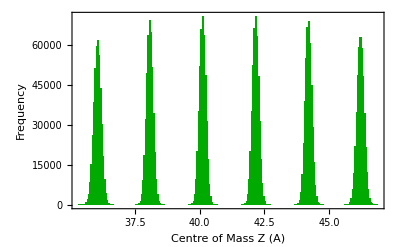

```mathematica
AgComzHistsyn100=Histogram[agzsyn100,300,ChartStyle->Darker[Green],Frame->True,FrameLabel->{"Centre of Mass Z (A)","Frequency"},LabelStyle->Directive[FontSize->15]]
```

```mathematica
topAgsurfacesyn100=Mean[Select[agzsyn100,#<37&]]
```

36.0559

```mathematica
pvpcomfromsurfsyn100=topAgsurfacesyn100-pvpcomsyn100;
oxyfromsurfsyn100=topAgsurfacesyn100-oxysyn100;
```

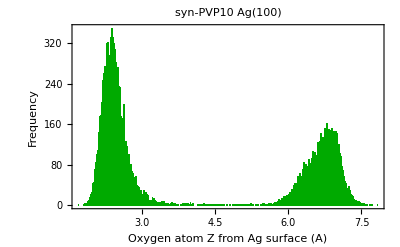

```mathematica
OxyHistsyn100=Histogram[Flatten[oxyfromsurfsyn100],300,ChartStyle->Darker[Green],Frame->True,FrameLabel->{"Oxygen atom Z from Ag surface (A)","Frequency"},LabelStyle->Directive[FontSize->15],PlotLabel->"syn-PVP10 Ag(100)"]
```

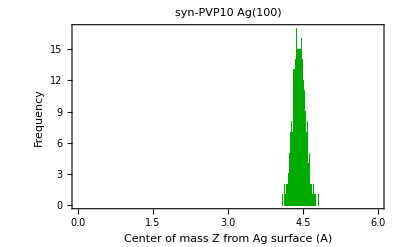

```mathematica
ComzHistsyn100=Histogram[Flatten[pvpcomfromsurfsyn100],300,ChartStyle->Darker[Green],Frame->True,FrameLabel->{"Center of mass Z from Ag surface (A)","Frequency"},LabelStyle->Directive[FontSize->15],PlotLabel->"syn-PVP10 Ag(100)",PlotRange->{{0,6},Full}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
CreateDirectory["compare_100111"];
```

CreateDirectory::filex: "E:\\scratch\\archive\\Ag_PVP10\\para\\111Ag\\pmf_curve\\equilibrate\\1_NVT\\compare_100111\\" already exists.

```mathematica
Export["compare_100111/Hist_Comz_syn100.png",ComzHistsyn100,ImageResolution->300];
Export["compare_100111/Hist_Oxy_syn100.png",OxyHistsyn100,ImageResolution->300];
```

```mathematica
SetDirectory["E:\\scratch\\archive\\Ag_PVP10\\isotac-para\\100Ag\\pmf_curve\\equilibrate\\1_NVT"]
```

E:\scratch\archive\Ag_PVP10\isotac-para\100Ag\pmf_curve\equilibrate\1_NVT

```mathematica
readtraj[];
```

```mathematica
pvpcomiso100=pvpcomtemp;
oxyiso100=oxytemp;
agziso100=agztemp;
```

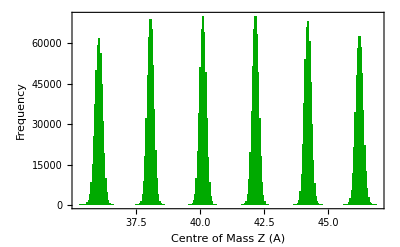

```mathematica
AgComzHistiso100=Histogram[agziso100,300,ChartStyle->Darker[Green],Frame->True,FrameLabel->{"Centre of Mass Z (A)","Frequency"},LabelStyle->Directive[FontSize->15]]
```

```mathematica
topAgsurfaceiso100=Mean[Select[agziso100,#<37&]]
```

36.0584

```mathematica
oxyfromsurfiso100=topAgsurfaceiso100-oxyiso100;
pvpcomfromsurfiso100=topAgsurfaceiso100-pvpcomiso100;
```

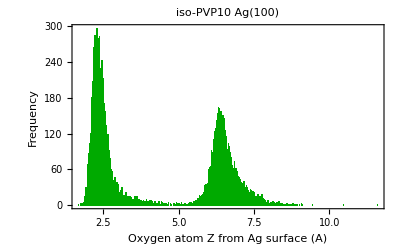

```mathematica
OxyHistiso100=Histogram[Flatten[oxyfromsurfiso100],300,ChartStyle->Darker[Green],Frame->True,FrameLabel->{"Oxygen atom Z from Ag surface (A)","Frequency"},LabelStyle->Directive[FontSize->15],PlotLabel->"iso-PVP10 Ag(100)"]
```

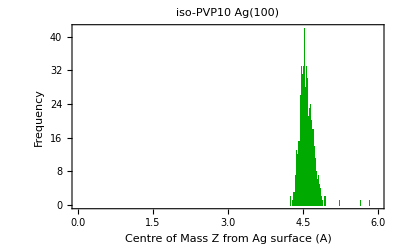

```mathematica
ComzHistiso100=Histogram[Flatten[pvpcomfromsurfiso100],300,ChartStyle->Darker[Green],Frame->True,FrameLabel->{"Centre of Mass Z from Ag surface (A)","Frequency"},LabelStyle->Directive[FontSize->15],PlotLabel->"iso-PVP10 Ag(100)",PlotRange->{{0,6},All}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["compare_100111/Hist_Comz_iso100.png",ComzHistiso100,ImageResolution->300];
Export["compare_100111/Hist_Oxy_iso100.png",OxyHistiso100,ImageResolution->300];
```

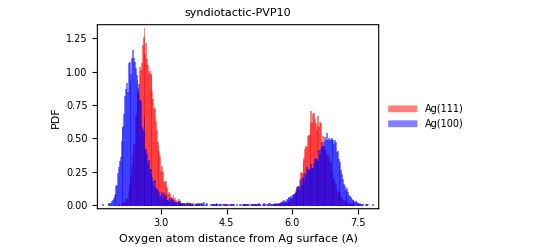

```mathematica
OxyHistCompsyn=Histogram[{Flatten[oxyfromsurf],Flatten[oxyfromsurfsyn100]},
300,"PDF",PlotLabel->"syndiotactic-PVP10",
ChartStyle->{Red,Blue},
ChartLegends->Placed[{"Ag(111)","Ag(100)"},Bottom],
Frame->True,
FrameLabel->{"Oxygen atom distance from Ag surface (A)","PDF"},
LabelStyle->Directive[FontSize->15]]
```

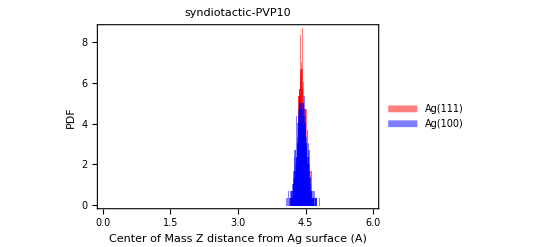

```mathematica
ComzHistCompsyn=Histogram[{Flatten[pvpcomfromsurf],Flatten[pvpcomfromsurfsyn100]},
300,"PDF",PlotLabel->"syndiotactic-PVP10",
ChartStyle->{Red,Blue},
ChartLegends->Placed[{"Ag(111)","Ag(100)"},Bottom],
Frame->True,
FrameLabel->{"Center of Mass Z distance from Ag surface (A)","PDF"},
LabelStyle->Directive[FontSize->15],PlotRange->{{0,6},Full}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["compare_100111/Hist_Comz_Compare_Syn.png",ComzHistCompsyn,ImageResolution->100];
Export["compare_100111/Hist_Oxy_Compare_Syn.png",OxyHistCompsyn,ImageResolution->100];
```

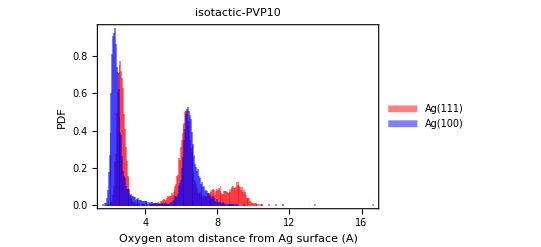

```mathematica
OxyHistCompiso=Histogram[{Flatten[oxyfromsurfiso],Flatten[oxyfromsurfiso100]},
300,"PDF",PlotLabel->"isotactic-PVP10",
ChartStyle->{Red,Blue},
ChartLegends->Placed[{"Ag(111)","Ag(100)"},Bottom],
Frame->True,
FrameLabel->{"Oxygen atom distance from Ag surface (A)","PDF"},
LabelStyle->Directive[FontSize->15]]
```

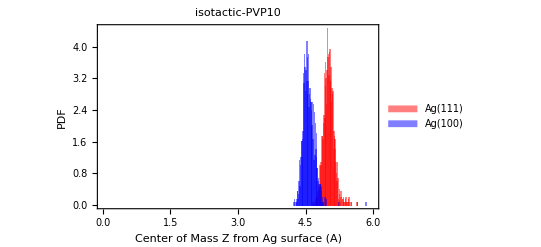

```mathematica
ComzHistCompiso=Histogram[{Flatten[pvpcomfromsurfiso],Flatten[pvpcomfromsurfiso100]},
300,"PDF",PlotLabel->"isotactic-PVP10",
ChartStyle->{Red,Blue},
ChartLegends->Placed[{"Ag(111)","Ag(100)"},Bottom],
Frame->True,
FrameLabel->{"Center of Mass Z from Ag surface (A)","PDF"},
LabelStyle->Directive[FontSize->15],PlotRange->{{0,6},Full}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["compare_100111/Hist_Comz_Compare_Iso.png",ComzHistCompiso,ImageResolution->100];
Export["compare_100111/Hist_Oxy_Compare_Iso.png",OxyHistCompiso,ImageResolution->100];
```

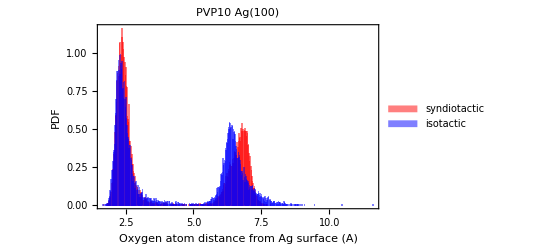

```mathematica
OxyHistComp=Histogram[{Flatten[oxyfromsurfsyn100],Flatten[oxyfromsurfiso100]},
300,"PDF",PlotLabel->"PVP10 Ag(100)",
ChartStyle->{Red,Blue},
ChartLegends->Placed[{"syndiotactic","isotactic"},Bottom],
Frame->True,
FrameLabel->{"Oxygen atom distance from Ag surface (A)","PDF"},
LabelStyle->Directive[FontSize->15]]
```

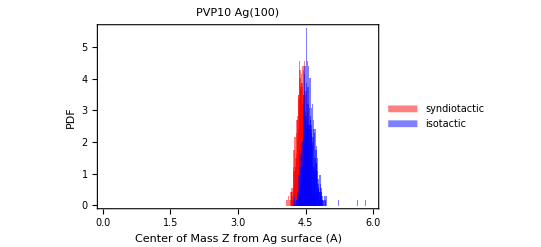

```mathematica
ComzHistComp=Histogram[{Flatten[pvpcomfromsurfsyn100],Flatten[pvpcomfromsurfiso100]},
300,"PDF",PlotLabel->"PVP10 Ag(100)",
ChartStyle->{Red,Blue},
ChartLegends->Placed[{"syndiotactic","isotactic"},Bottom],
Frame->True,
FrameLabel->{"Center of Mass Z from Ag surface (A)","PDF"},
LabelStyle->Directive[FontSize->15],PlotRange->{{0,6},Full}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["density/Hist_Comz_Compare_100.png",ComzHistComp,ImageResolution->100];
Export["density/Hist_Oxy_Compare_100.png",OxyHistComp,ImageResolution->100];
```